```mathematica
ClearAll;
```

```mathematica
<<IGraphM``
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

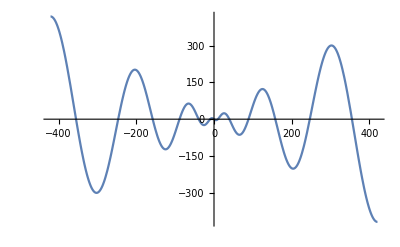

-Graphics3D-

```mathematica
(*Schwefel' s Function*)
fun4Name="Schwefel' s Function";
fun4[x_]:=Module[{l=Length@x}, Sum[-x[[i]] Sin[Sqrt[Abs[x[[i]]]]], {i,l}]];
Plot[fun4@{x},{x,-420.969,420.969}]
Plot3D[fun4@{x1,x2},{x1,-420.969,420.969},{x2,-420.969,420.969}]
```

```mathematica
draw[matrix_]:=Module[{f,g,adjacencyMatrix,vertices},
adjacencyMatrix=matrix;
adjacencyMatrix=Rescale@adjacencyMatrix/. 0->∞//N;
f[pts_List,e_]:=Block[
{s=0.015,weight=PropertyValue[{g,e},EdgeWeight]},
{
ColorData["TemperatureMap"][weight],
Arrowheads[{{s,0.1},{s,0.9}}],
AbsoluteThickness[weight*15],
Arrow[pts]
}
];

vertices=Join[{{0,0}},Table[{4 Cos[a],4 Sin[a]},{a,Pi/4,2 Pi,Pi/4}],Table[{7 Cos[a],7 Sin[a]},{a,0,5 Pi/3,Pi/6}]][[1;;Length@adjacencyMatrix]];
g=WeightedAdjacencyGraph[adjacencyMatrix,
VertexLabels->"Name",
EdgeLabels->(*"EdgeWeight"*)None,
EdgeShapeFunction->f,
VertexLabelStyle->Directive[Black,Bold,20],
ImageSize->Large,
Background->GrayLevel@0.8,
VertexCoordinates->vertices
(*,
VertexCoordinates->vertices*)
];
Return@g;
];
```

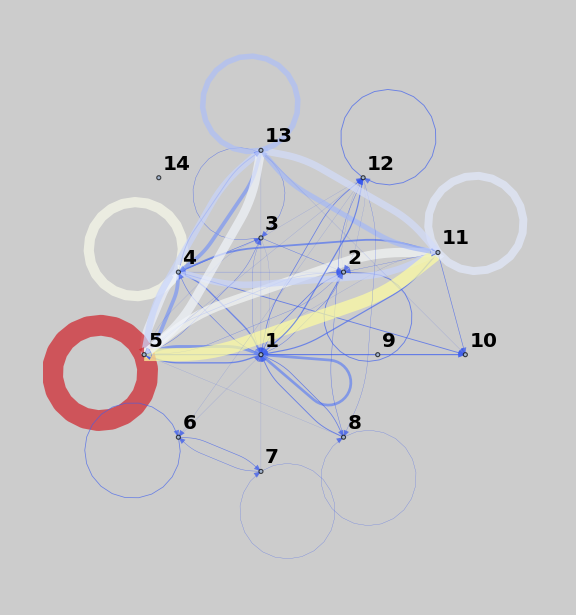

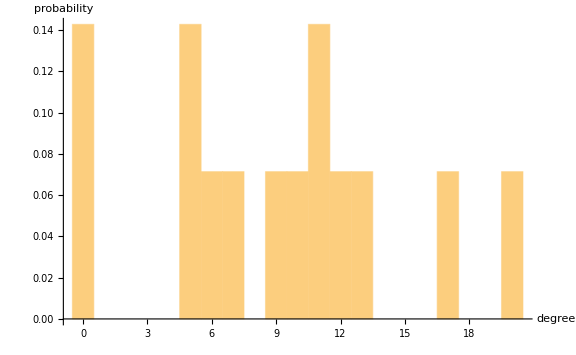

```mathematica
realData={
	{18,5,2,  4 ,   9,  0,  0,  5, 0, 3,   1,   5,    0,   0},
	{  3,6,0,  2 ,   2,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  1,3,3,  4 ,   3,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  9,0,0, 68,  25,  0,  0,  0, 0, 6,  12,   0,   6,    0},
	{19,4,1,57, 139,  0,  0, 0, 0, 7,  62,  0,  44,  0},
	{  1,0,0,  0 ,   0,  5,  4,  0, 0,  0,   0,    0,   0,   0},
	{  1,0,0,  0 ,   0,  3,  2,  0, 0,  0,   0,    0,   0,   0},
	{  6,0,0,  0 ,   1,  0,  0,  2, 0,  0,   0,    3,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  8,2,0,44 , 85, 0,  0,  0, 0,  4,  53,   0,  35,  0},
	{  8,1,0,  0 ,   1,  1,  0,  2, 0,  0,   0,    6,   0,   0},
	{  1,0,0, 25 , 59,  0,  0, 0, 0,  1,  47,   0,  37,  0},
	{  0,0,0,  0 ,   0,   0,  0,  0, 0,  0,    0,    0,   0,   0} };
realData=realData[[All,1;;Length@realData]];
g1=draw@realData
Histogram[VertexDegree[g1],{1},"Probability",AxesLabel->{"degree","probability"}]
```

```mathematica
Clear[pts];
pts[m_,r_]:=Module[{pts,DCr, DCm, CCr,CCm,BCm, BCr, EVCr, EVCm, ICr, ICm},
pts=0;

DCm = Mean[DegreeCentrality@IGWeightedAdjacencyGraph@m];
DCr = Mean[DegreeCentrality@IGWeightedAdjacencyGraph@r];

CCm=Mean[ClosenessCentrality@IGWeightedAdjacencyGraph@m];
CCr=Mean[ClosenessCentrality@IGWeightedAdjacencyGraph@r];

BCm=Mean[IGBetweenness@IGWeightedAdjacencyGraph@m];
BCr=Mean[IGBetweenness@IGWeightedAdjacencyGraph@r];

EVCm=Mean[IGEigenvectorCentrality@WeightedAdjacencyGraph@m];
EVCr=Mean[IGEigenvectorCentrality@WeightedAdjacencyGraph@r];
(*Information centrality*)
pts=((DCr-DCm)/DCr)^2+((CCr-CCm)/CCr)^2+((BCr-BCm)/BCr)^2+((EVCr-EVCm)/EVCr)^2;
pts*=1000;
Return@pts
];
```

gBestPositionIndex initial = 13

gBestPosition before loop = {4.34379,4.58102,1.71287,-3.29056,0.902676}

swarmPosition before loop = {{3.29187,-1.5966,1.31615,-3.52533,0.43464},{-1.78477,2.65731,4.7662,-0.925051,-1.44646},{-3.85,-0.529962,0.955932,-4.44973,-4.28267},{4.26365,-2.18196,4.03257,2.57626,-2.11146},{2.49727,1.70896,2.0706,-4.80311,-4.72454},{-4.65384,-4.7894,-3.19285,-1.28778,-1.4162},{2.67078,4.57655,-1.18993,-1.30149,-1.13005},{-4.4315,2.45379,0.757462,-2.34644,2.88202},{3.53901,-3.57476,-3.3898,1.59384,-4.39862},{-1.93173,-4.47945,3.50623,-0.910621,-4.94119},{-0.172601,0.69461,-0.0611772,-2.31902,-4.853},{-0.146502,-4.47661,-4.7635,-0.426783,-2.01302},{4.34379,4.58102,1.71287,-3.29056,0.902676},{-3.48774,-2.58435,0.64743,-3.99168,4.05434}}

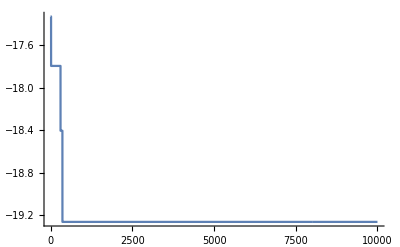

```mathematica
Clear[adjCitationData];
Clear[inertia];
Clear[swarmPosition];
Clear[swarmVelocity];
Clear[pBestPosition];
Clear[pBestCost];
Clear[swarmPositionCostTemp];
Clear[swarmPositionTemp];
Clear[swarmPositionCost];
Clear[gBestPosition];
Clear[gBestCost];
Clear[boundry];
Clear[historyGBestCost];
Clear[historyGBestPosition];

Clear[f];
Clear[fLowerBound];
Clear[fUpperBound];
Clear[swarmDim];
Clear[NP];
Clear[c1];
Clear[c2];
Clear[w];
Clear[iterations];

PSOAlgorithm[f_, fLimit_, swarmDim_, NP_, c1_, c2_, w_, iterations_
]:=Module[
{
inertia,swarmPosition,swarmPositionTemp,swarmVelocity,pBestPosition,
pBestCost,swarmPositionCost,swarmPositionCostTemp,gBestPosition,gBestPositionIndex,
gBestCost,FitnessFunction,fLowerBound,fUpperBound,f1,
rand1,
rand2,
i,j,k,n,l,
boundry,
historyGBestPosition,historyGBestCost,communicationList,
it
},

inertia=ConstantArray[0,{NP,swarmDim}];
swarmPosition=ConstantArray[0,{NP,swarmDim}];
swarmPositionTemp={};
swarmVelocity=ConstantArray[0,{NP,swarmDim}];
pBestPosition=ConstantArray[0,{NP,swarmDim}];
pBestCost=Table[0,NP];
swarmPositionCostTemp=Table[0,swarmDim];
swarmPositionCost=Table[0,NP];
swarmPositionCostTemp=0;
gBestPosition=Table[0,swarmDim];
gBestCost=0;
gBestPositionIndex;
FitnessFunction=f;
f1=FitnessFunction;
fLowerBound=fLimit[[1]];
fUpperBound=fLimit[[2]];
boundry={};
historyGBestPosition={};
historyGBestCost={};
communicationList={};

(*Initialization start*)
swarmPosition=RandomReal[{fLowerBound,fUpperBound},{NP,swarmDim}];(*Initial position of each particle is set at random*)
swarmVelocity=ConstantArray[0,{NP,swarmDim}];(*Initial velocity of each particle is set to 0*)
pBestPosition=swarmPosition;
f1[x__]:=Re[Map[FitnessFunction,{x}]];

swarmPositionCost=Table[f1[swarmPosition[[n]]],{n,NP}];
pBestCost=swarmPositionCost;
gBestCost=Min[pBestCost];
gBestPosition=pBestPosition[[First@First@Position[swarmPositionCost,gBestCost]]];
gBestPositionIndex=First@First@Position[swarmPositionCost,gBestCost];
Print["gBestPositionIndex initial = ", gBestPositionIndex];
Print["gBestPosition before loop = " ,gBestPosition];
Print["swarmPosition before loop = " ,swarmPosition];

(*Main Loop*)

it=0;
While[it< iterations,
{

(*Update the velocity and position vectors*)
For[i=1,i≤  (NP),i++,
For[j=1,j≤  (swarmDim),j++,
rand1=RandomReal[{0,1}];
rand2=RandomReal[{0,1}];
inertia=w*swarmVelocity[[i]][[j]];
swarmVelocity[[i]]= inertia + (c1 * rand1 * (pBestPosition[[i]][[j]]- swarmPosition[[i]][[j]]))+
(c2 *rand2 * (gBestPosition - swarmPosition[[i]][[j]]));
];

(*Update the particle's position*)
swarmPosition[[i]] +=swarmVelocity[[i]];
For[j=1,j<=swarmDim,j++,
If[swarmPosition[[i,j]]<fLowerBound,swarmPosition[[i,j]]=RandomReal@fLimit];
If[swarmPosition[[i,j]]>fUpperBound,swarmPosition[[i,j]]=RandomReal@fLimit];
];
n=0;
f1[x__]:=Map[FitnessFunction,{x}];
swarmPositionCost=Table[f1[swarmPosition[[n]]],{n,NP}];

(*Update pBest and gBest*)
If[swarmPositionCost[[i]]<= pBestCost[[i]],
{
pBestCost[[i]]=swarmPositionCost[[i]];
pBestPosition[[i]]=swarmPosition[[i]];
If[pBestCost[[i]]<= gBestCost,
{
(*Print@"----Particle updating the gBest-------";*)
(*Capture here*)
(*Here link is created in two cases: 
	1. When particle replaces the gBest, a link is created between particle at current position and the particle at gBest position.
	2. A link is also created between the particle at current position and all the other particles in the swarm. 
*)
AppendTo[communicationList,First@First@Position[swarmPosition, pBestPosition[[i]] ]<-> gBestPositionIndex]; 
For[l=1,l<=Length@swarmPosition ,l++,
If[l== gBestPositionIndex, Continue[]];(*This is to avoid double connection between gBest and current particle position*)
	AppendTo[communicationList, i <-> l];
];
gBestCost=pBestCost[[i]];
gBestPosition=pBestPosition[[i]];
gBestPositionIndex=First@First@Position[swarmPosition, pBestPosition[[i]] ];
};
];
}
];
];
AppendTo[historyGBestPosition,gBestPosition];
AppendTo[historyGBestCost,gBestCost];
,it++
}];
Return@{swarmPosition, pBestPosition,pBestCost,gBestPosition,gBestCost ,historyGBestPosition, historyGBestCost, communicationList, swarmPositionCost};
];
(*PSOAlgorithm[f_, fLimit_, swarmDim_, NP_, c1_, c2_, w_, iterations_]*)
(*outputFromPso=PSOAlgorithm[fun4,{-5,5} ,3,14,1.49445,1.49445,0.729,40000];*)
outputFromPso=PSOAlgorithm[fun4,{-5,5} ,5,14,1.49445,1.49445,0.729,10000];
ListPlot[outputFromPso[[7]],Joined->True]

(*outputFromPso=PSOAlgorithm[fun3,{-5,5} ,3,14,-420.969,420.969,0.729,100];
ListPlot[outputFromPso[[7]],Joined->True]*)
```

```mathematica
capturedDataFromPSO=outputFromPso[[8]];
capturedDataFromPSO
```

{1<->13,1<->1,1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,1<->8,1<->9,1<->10,1<->11,1<->12,1<->14,3<->1,3<->2,3<->3,3<->4,3<->5,3<->6,3<->7,3<->8,3<->9,3<->10,3<->11,3<->12,3<->13,3<->14,8<->3,8<->1,8<->2,8<->4,8<->5,8<->6,8<->7,8<->8,8<->9,8<->10,8<->11,8<->12,8<->13,8<->14,10<->8,10<->1,10<->2,10<->3,10<->4,10<->5,10<->6,10<->7,10<->9,10<->10,10<->11,10<->12,10<->13,10<->14,12<->10,12<->1,12<->2,12<->3,12<->4,12<->5,12<->6,12<->7,12<->8,12<->9,12<->11,12<->12,12<->13,12<->14,7<->12,7<->1,7<->2,7<->3,7<->4,7<->5,7<->6,7<->7,7<->8,7<->9,7<->10,7<->11,7<->13,7<->14,10<->7,10<->1,10<->2,10<->3,10<->4,10<->5,10<->6,10<->8,10<->9,10<->10,10<->11,10<->12,10<->13,10<->14}

```mathematica
sortedCapturedDataFromPSO = Sort[capturedDataFromPSO,#1[[1]]<#2[[1]]&]
```

{1<->14,1<->12,1<->11,1<->10,1<->9,1<->8,1<->7,1<->6,1<->5,1<->4,1<->3,1<->2,1<->1,1<->13,3<->14,3<->13,3<->12,3<->11,3<->10,3<->9,3<->8,3<->7,3<->6,3<->5,3<->4,3<->3,3<->2,3<->1,7<->14,7<->13,7<->11,7<->10,7<->9,7<->8,7<->7,7<->6,7<->5,7<->4,7<->3,7<->2,7<->1,7<->12,8<->14,8<->13,8<->12,8<->11,8<->10,8<->9,8<->8,8<->7,8<->6,8<->5,8<->4,8<->2,8<->1,8<->3,10<->14,10<->13,10<->12,10<->11,10<->10,10<->9,10<->8,10<->6,10<->5,10<->4,10<->3,10<->2,10<->1,10<->7,10<->14,10<->13,10<->12,10<->11,10<->10,10<->9,10<->7,10<->6,10<->5,10<->4,10<->3,10<->2,10<->1,10<->8,12<->14,12<->13,12<->12,12<->11,12<->9,12<->8,12<->7,12<->6,12<->5,12<->4,12<->3,12<->2,12<->1,12<->10}

```mathematica
matrixFormSortedCapturedDataFromPSO = AdjacencyMatrix@capturedDataFromPSO //MatrixForm
```

(1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 3 | 1 | 2 | 1
1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 1 | 0
2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 3 | 1 | 2 | 1
1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 1 | 0
2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 3 | 1 | 2 | 1
2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 3 | 1 | 2 | 1
1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 1 | 0
3 | 2 | 2 | 3 | 2 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 2
1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 1 | 0
2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 3 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 1 | 0)

```mathematica
testList=AdjacencyMatrix@sortedCapturedDataFromPSO;
```

```mathematica
capturedFromPSO={};
For[i=1,i<=Length@testList,i++,

subList={};
For[j=1,j<=Length@testList,j++,
If[i==j,testList[[i]][[j]]=0];(*avoiding self looping in captured data*)
AppendTo[subList, testList[[i]][[j]]];
];
AppendTo[capturedFromPSO, subList];
];
capturedFromPSO
```

{{0,1,2,1,3,1,2,2,1,1,1,2,1,1},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{2,1,0,1,3,1,2,2,1,1,1,2,1,1},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{3,2,3,2,0,2,3,3,2,2,2,3,2,2},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{2,1,2,1,3,1,0,2,1,1,1,2,1,1},{2,1,2,1,3,1,2,0,1,1,1,2,1,1},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{2,1,2,1,3,1,2,2,1,1,1,0,1,1},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{1,0,1,0,2,0,1,1,0,0,0,1,0,0}}

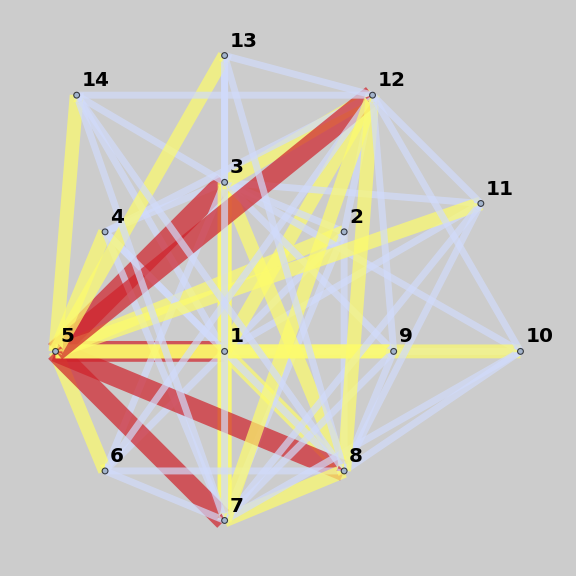

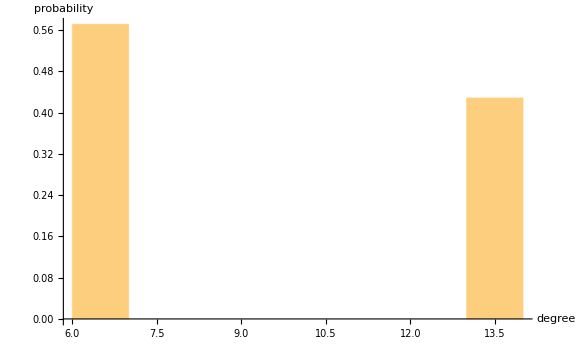

```mathematica
capturedFromPSO=capturedFromPSO[[All,1;;Length@capturedFromPSO]];
g1=draw@capturedFromPSO
Histogram[VertexDegree[g1],{1},"Probability",AxesLabel->{"degree","probability"}]
```

```mathematica
For[i=1,i<=Length@realData,i++,
For[j=1,j<=Length@realData,j++,
If[i==j,realData[[i]][[j]]=0];(*avoiding self looping in captured data*)
];
];
```

```mathematica
realData (*real data WITHOUT self looping*)
```

{{0,5,2,4,9,0,0,5,0,3,1,5,0,0},{3,0,0,2,2,0,0,0,0,0,0,1,0,0},{1,3,0,4,3,0,0,0,0,0,0,1,0,0},{9,0,0,0,25,0,0,0,0,6,12,0,6,0},{19,4,1,57,0,0,0,0,0,7,62,0,44,0},{1,0,0,0,0,0,4,0,0,0,0,0,0,0},{1,0,0,0,0,3,0,0,0,0,0,0,0,0},{6,0,0,0,1,0,0,0,0,0,0,3,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{8,2,0,44,85,0,0,0,0,4,0,0,35,0},{8,1,0,0,1,1,0,2,0,0,0,0,0,0},{1,0,0,25,59,0,0,0,0,1,47,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

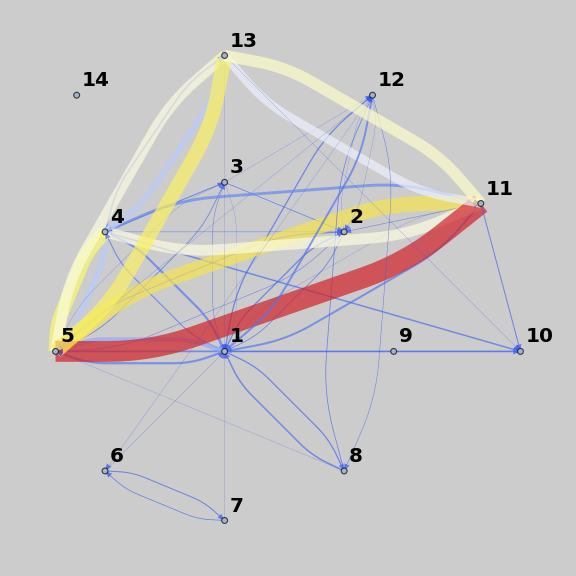

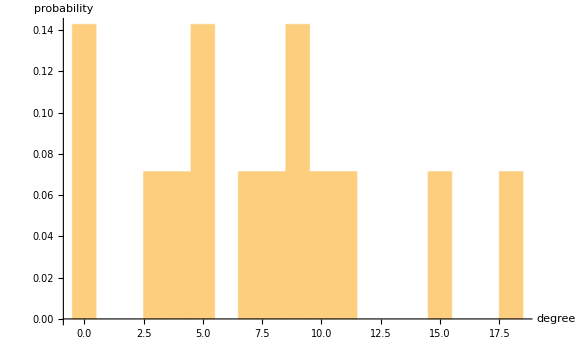

```mathematica
realData=realData[[All,1;;Length@realData]];
g1=draw@realData
Histogram[VertexDegree[g1],{1},"Probability",AxesLabel->{"degree","probability"}]
```

```mathematica
capturedFromPSO
```

{{0,1,2,1,3,1,2,2,1,1,1,2,1,1},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{2,1,0,1,3,1,2,2,1,1,1,2,1,1},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{3,2,3,2,0,2,3,3,2,2,2,3,2,2},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{2,1,2,1,3,1,0,2,1,1,1,2,1,1},{2,1,2,1,3,1,2,0,1,1,1,2,1,1},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{2,1,2,1,3,1,2,2,1,1,1,0,1,1},{1,0,1,0,2,0,1,1,0,0,0,1,0,0},{1,0,1,0,2,0,1,1,0,0,0,1,0,0}}

```mathematica
pts[capturedFromPSO,realData]
```

7319.61